# MGDrivE: Software Paper Data Analysis

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_]:=Module[{plotRight,plotLeft},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameLabel->(Style[#,30]&/@plotLabels)
]
]
Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
AddLabelsToReshapedDataNode[reshapedDataNode_,genotypes_,patchNumber_]:=Module[{breakdownWithPop,breakdownWithTime,labels},
breakdownWithPop=Prepend[#,patchNumber]&/@reshapedDataNode[[All,2;;All]];
breakdownWithTime=Prepend[#[[2]],#[[1]]]&/@Transpose[{Range[breakdownWithPop//Length],breakdownWithPop}];
labels=Prepend[ReplacePart[genotypes,1->"Patch"],"Time"];
Prepend[breakdownWithTime,labels]
]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,3;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,3;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,3;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Gray]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->40,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]


ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
Yellow,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+2*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+2*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{ImageRotate[barChart,90Degree]//Show[#]&,dayCount//Show[#]&,network//Show[#]&,popCount//Show[#]&,ImageRotate[flow,90Degree]//Show[#]&}}];
Rasterize[row]
]
GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_},ticks_]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicks->ticks,
FrameTicksStyle->50,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
FrameLabel->{{Style["",35],None},{Style["Time (days)",50],""}},
BarSpacing->{0,0},
AspectRatio->1/3,
PlotRangePadding->{0,0},
BarOrigin->Bottom,
ImageSize->1000(*frameDimensions[[1]]*) ,
Epilog->Flatten[{Lighter[Gray,.5],Thickness[.0005],Opacity[.5],(Line[{{#,0},{#,maxPop}}]&/@Range[0,ticksMax,250]),(Line[{{0,#},{ticksMax,#}}]&/@Range[0,maxPop,1000])}]
]
]
PlotDynamics[data_,ranges_,colorPalette_,plotLabels_,tag_]:=Module[{plotRight,plotLeft},
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1,
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->Large,
PlotRange->{{0,ranges[[1]]},{0,ranges[[2]]}},
FrameStyle->{
{Thick,Thick},
{Thick,Thick}
},
FrameTicks->Automatic,
FrameTicksStyle->Directive[Gray,18],
FrameLabel->(Style[#,40]&/@plotLabels),
Epilog->Style[Text[tag,{900,550}],Directive[Gray,35]]
]
]
CreateColorBlend[genotypes_,colorSchemeName_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeName][#]&/@Range[0,1,1/(Length[genotypes]-1)],Lighter[Black,.75]];
colorPairs=Transpose[{Prepend[genotypes[[All,1]],"Total"],colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
```

## Paper Plots

Replacement Deterministic

```mathematica
baseFolder="ReplacementDeterministic/";
```

## Load Data

```mathematica
(*Load data*)
(*folder=FileNames["0*",baseFolder]
dataTotal=Table[
{genotypes,dataTemp}=ImportAndReshapeData[folder[[i]]];
dataTemp
,{i,1,Length[folder]}];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
(*Reshape data and calculate desired quantile*)
quantile=1/2;
reshapedData={reshapedDataMale,reshapedDataFemale}=ReshapeStochasticMultiNode[dataTotal,1/2];
reshapedDataTotal=reshapedDataMale+reshapedDataFemale;*)
```

## Export Median Data

```mathematica
(*path=baseFolder<>"Median/0001"
ParallelTable[
malesPop=AddLabelsToReshapedDataNode[reshapedDataMale[[i]],genotypes,i];
fileName=path<>"/ADM_Run1_Patch"<>StringPadLeft[ToString[i],6,"0"]<>".csv";
Export[fileName,malesPop]
,{i,1,reshapedDataMale//Length}];
ParallelTable[
femalesPop=AddLabelsToReshapedDataNode[reshapedDataFemale[[i]],genotypes,i];
fileName=path<>"/AF1_Aggregate_Run1_"<>StringPadLeft[ToString[i],6,"0"]<>".csv";
Export[fileName,femalesPop]
,{i,1,reshapedDataFemale//Length}];*)
```

## FlowChart

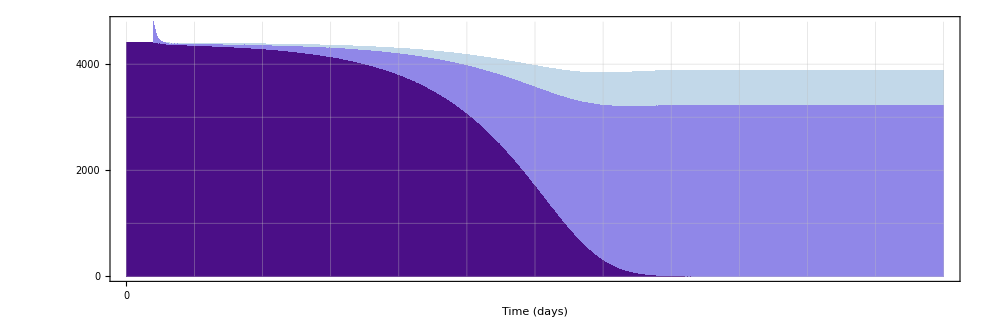

swatch.pdf

```mathematica
framesRange={1,3000};
(*genotypesIndicesToAggregate={{"WW",{1}},{"WH",{2}},{"WR",{3}},{"WB",{4}},{"HH",{5}},{"HR",{6}},{"HB",{7}},{"RR",{8}},{"RB",{9}},{"BB",{10}}}*)
genotypesIndicesToAggregate={
{"W",{1,1,2,3,4}},
{"H",{2,5,5,6,7}},
{"R",{3,6,8,8,9}},
{"B",{4,7,9,10,10}}
};
(*Setup color palette*)
selectedGenotypes=Prepend[genotypesIndicesToAggregate[[All,1]],"Total"];
{colorPalette,colorSwatch}=CreateColorBlend[genotypesIndicesToAggregate,"LakeColors",{20,15}];
colorPalette=Darker[#,0.0]&/@ReplacePart[colorPalette,{1->Black(*,4->Lighter[Magenta,.8]*)}];
colorSwatch=SwatchLegend[colorPalette,selectedGenotypes,LabelStyle->{FontSize->20},LegendMarkerSize->25,LegendLayout->{"Column",1}]
(*Generate plot*)
{frameDimensions,scaler,resolution,colorScheme,nodeScaler}={{2000,1440/2560*2000},3.5,500,"LakeColors",1};
{{maleDatasets,femaleDatasets},{genotypes,ticksMax,{maleMax,femaleMax}}}=ImportAndReshapeMosquitoDatasets[baseFolder<>"Median/0001",{"ADM","AF1"}];
totalPopulationDatasets=(maleDatasets+femaleDatasets);
{aggregatedLabels,aggregatedPopulations}=AggregatePopulationByGenotypeIndices[totalPopulationDatasets,genotypesIndicesToAggregate];
aggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[aggregatedPopulations];
{labels,colors}={genotypesIndicesToAggregate[[All,1]],Lighter[#,0]&/@(colorPalette//RotateLeft)};
maxPop=Flatten[aggregatedPopulationsAcrossNodes]//Max;
barChartPopDynReplacement=Map[
BarChartPopDynamicsFrames[#,aggregatedPopulationsAcrossNodes,{colors,maxPop,ticksMax,frameDimensions,labels},{{Range[0,2*maxPop,2000],None},{Range[0,50000,1000],None}}]&,
{ticksMax}
]
(*Export["FlowFull_Suppression.pdf",barChartPopDynReplacement[[1]],ImageResolution->300,ImageSize->frameDimensions[[1]]]*)
Export["swatch.pdf",colorSwatch]
```

## BleedPlot

```mathematica
(*Load and reshape data*)
dataFolder=baseFolder<>"Median/";
folder=FileNames["0*",dataFolder]
nodesData=Table[
{genotypes,dataTotal}=ImportAndReshapeData[folder[[i]]];
dataTotal
,{i,1,folder//Length}];
(*{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];*)
{repetition}={1};
{male,female}={1,2};
breakdowns=Table[
totalPopulation=nodesData[[repetition,male,i]]+nodesData[[repetition,female,i]]
,{i,1,nodesData[[1,1]]//Length}];
popMax=breakdowns[[2;;All]]//Flatten//Max;
indicesSelection=Range[genotypesIndicesToAggregate//Length];
```

{ReplacementDeterministic/Median/0001}

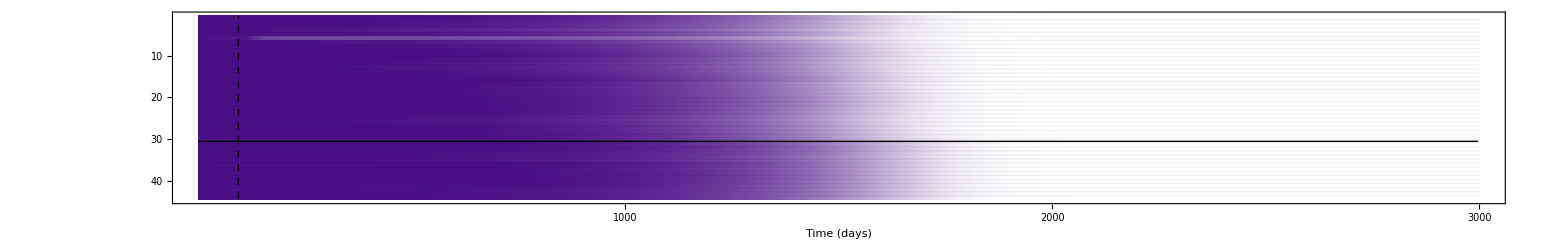
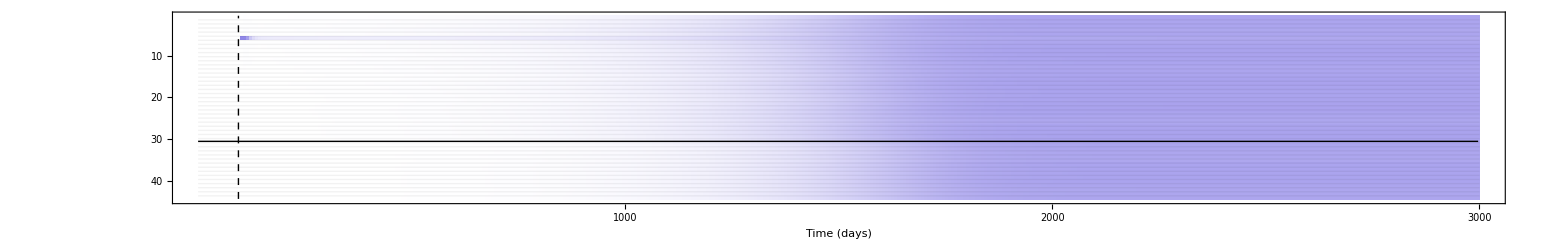
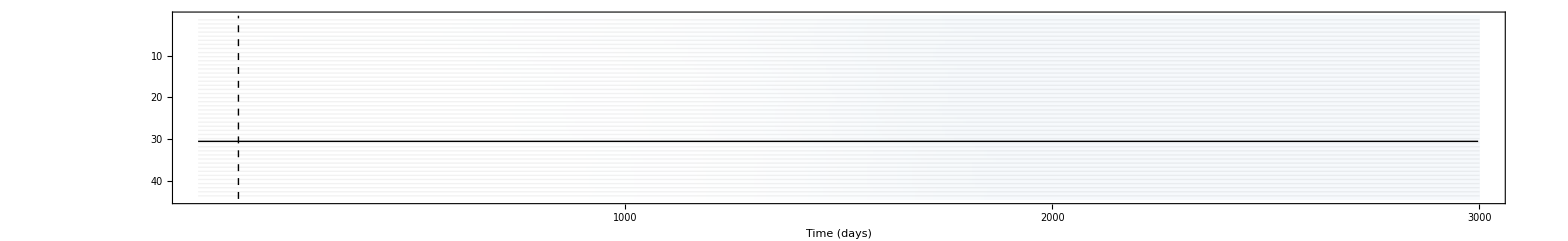
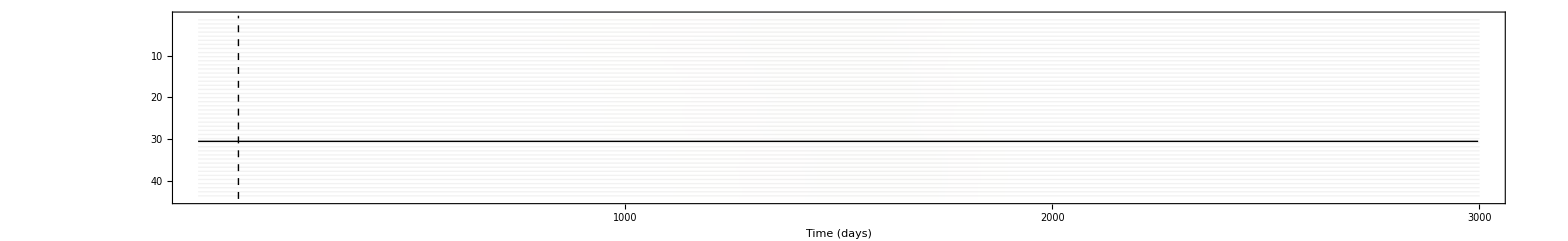

```mathematica
genotypesPlotsReplacement=Table[
frameTicks={{Automatic,None},{Automatic,Automatic}};
MatrixPlot[Transpose[aggregatedPopulations][[All,All,indicesSelection[[i]]]]//Transpose
,AspectRatio->1/6.5
,Frame->True
,FrameStyle->Directive[Black,Thick]
,ImageSize->2000
,FrameTicks->frameTicks
,FrameTicksStyle->Directive[Black,50]
,PlotRangePadding->None
,Mesh->{44,0}
,MeshStyle->Directive[Opacity[.05]]
,ColorFunction->(Blend[{White,colorPalette[[i+1]]},1.5*#1/popMax]&)(*ColorData[{"CherryTones",{1*breakdowns//Flatten//Max,0}}]*)
,ColorFunctionScaling->False
,Epilog->{Thick,Line[{{0,44-30},{428.5,44-30}}],Dashed,Line[{{13.5,.25},{13.5,44}}]}
,FrameLabel->{{Style["Time (days)",50],Style["Time (days)",50]},{Style["\n",35],None}}
]
,{i,1,indicesSelection//Length}];
bleedReplacement=genotypesPlotsReplacement
```

## Both

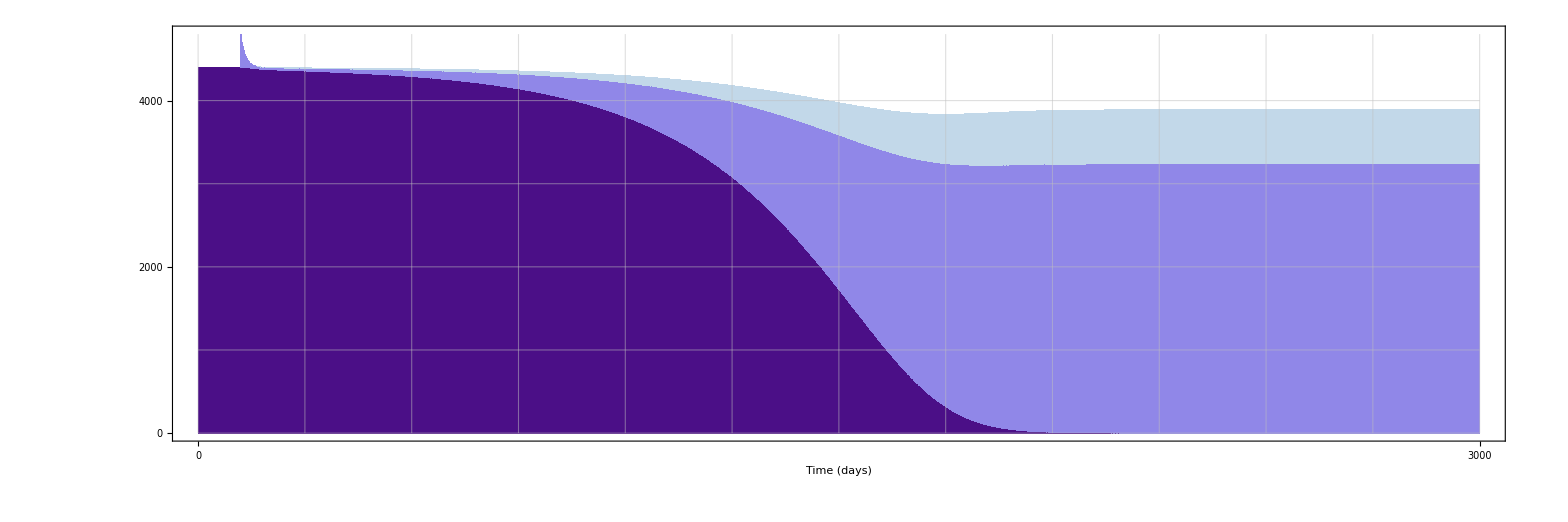
Population Size | -Graphics- | 
 |  | 
 | -Graphics- | W Allele
Metapopulation | -Graphics- | H Allele
 | -Graphics- |          R Allele

```mathematica
bleedPlots=Append[Show[#,FrameTicks->False,Frame->False,ImagePadding->{{45,19},{20,2.5}}]&/@bleedReplacement[[1;;3]],Show[bleedReplacement[[4]],ImagePadding->{{45,19},{20,2.5}}]];
gridReplacement=Grid[{
{Rotate[Style["Population Size",50,FontFamily->"Arial"],90Degree],barChartPopDynReplacement[[1]]//Show[#,ImageSize->2000,ImagePadding->{{120,60},{125,10}}]&,""},
{},
{Rotate[Style["",40,FontFamily->"Arial"],90Degree],bleedReplacement[[1]]//Show[#,ImagePadding->{{120,60},{2.5,2}}]&,Rotate[Style["W Allele",45,FontFamily->"Arial"],90Degree]},
{Rotate[Style["Metapopulation",50,FontFamily->"Arial"],90Degree],bleedReplacement[[2]]//Show[#,ImagePadding->{{120,60},{2.5,2}}]&,Rotate[Style["H Allele",45,FontFamily->"Arial"],90Degree]},
{Rotate[Style["",40,FontFamily->"Arial"],90Degree],bleedReplacement[[3]]//Show[#,ImagePadding->{{120,60},{125,2}}]&,Rotate[Style["         R Allele",45,FontFamily->"Arial"],90Degree]}
(*{Rotate[Style["2.d",60],90Degree],bleedReplacement[[4]]//Show[#,ImagePadding->{{45,19},{2.5,2.5}}]&},*)
(*{Rotate[Style["Total",40],90Degree],Show[ImageMultiply@@(Rasterize[#,RasterSize->2000,ImageResolution->10000]&/@bleedPlots),ImageSize->2000]}*)
}
,Frame->{
None,None,
{
{{1,1},{1,2}}->True,
{{2,5},{1,2}}->True
}
}
,FrameStyle->Directive[Opacity[0],LightGray,Thick]
]
(*Export["gridReplacement.pdf",gridReplacement]*)
```

Suppression Stochastic

```mathematica
baseFolder="SuppressionStochastic/";
```

## Load Data

```mathematica
(*Load data*)
(*folder=FileNames["0*",baseFolder]
dataTotal=Table[
{genotypes,dataTemp}=ImportAndReshapeData[folder[[i]]];
dataTemp
,{i,1,Length[folder]}];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
(*Reshape data and calculate desired quantile*)
quantile=1/2;
reshapedData={reshapedDataMale,reshapedDataFemale}=ReshapeStochasticMultiNode[dataTotal,1/2];
reshapedDataTotal=reshapedDataMale+reshapedDataFemale;*)
```

## Export Median Data

```mathematica
(*path=baseFolder<>"Median/0001"
ParallelTable[
malesPop=AddLabelsToReshapedDataNode[reshapedDataMale[[i]],genotypes,i];
fileName=path<>"/ADM_Run1_Patch"<>StringPadLeft[ToString[i],6,"0"]<>".csv";
Export[fileName,malesPop]
,{i,1,reshapedDataMale//Length}];
ParallelTable[
femalesPop=AddLabelsToReshapedDataNode[reshapedDataFemale[[i]],genotypes,i];
fileName=path<>"/AF1_Aggregate_Run1_"<>StringPadLeft[ToString[i],6,"0"]<>".csv";
Export[fileName,femalesPop]
,{i,1,reshapedDataFemale//Length}];*)
```

## FlowChart

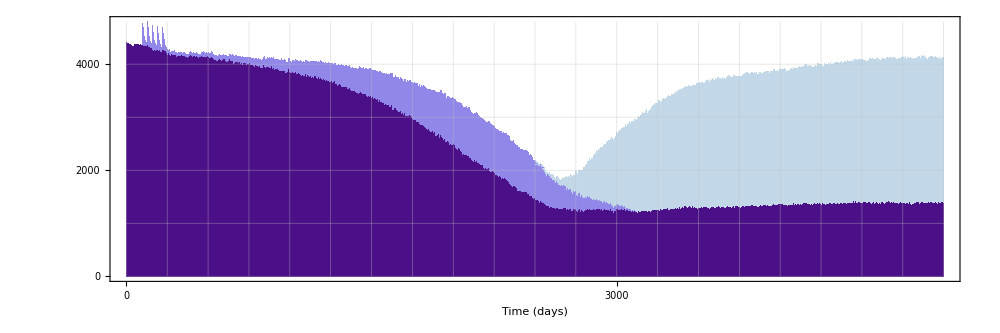

```mathematica
(*-----------------------------*)
framesRange={1,5000};
(*genotypesIndicesToAggregate={{"WW",{1}},{"WH",{2}},{"WR",{3}},{"WB",{4}},{"HH",{5}},{"HR",{6}},{"HB",{7}},{"RR",{8}},{"RB",{9}},{"BB",{10}}}*)
genotypesIndicesToAggregate={
{"W",{1,1,2,3,4}},
{"H",{2,5,5,6,7}},
{"R",{3,6,8,8,9}},
{"B",{4,7,9,10,10}}
};
(*Setup color palette*)
selectedGenotypes=Prepend[genotypesIndicesToAggregate[[All,1]],"Total"];
{colorPalette,colorSwatch}=CreateColorBlend[genotypesIndicesToAggregate,"LakeColors",{20,15}];
colorPalette=Lighter[#,0]&/@ReplacePart[colorPalette,{1->Black}];
colorSwatch=SwatchLegend[colorPalette,selectedGenotypes,LabelStyle->{FontSize->20},LegendMarkerSize->25,LegendLayout->{"Column",1}]
(*Generate plot*)
{frameDimensions,scaler,resolution,colorScheme,nodeScaler}={{2560,1440},3.5,500,"LakeColors",1};
{{maleDatasets,femaleDatasets},{genotypes,ticksMax,{maleMax,femaleMax}}}=ImportAndReshapeMosquitoDatasets[baseFolder<>"Median/0001",{"ADM","AF1"}];
totalPopulationDatasets=(maleDatasets+femaleDatasets);
{aggregatedLabels,aggregatedPopulations}=AggregatePopulationByGenotypeIndices[totalPopulationDatasets,genotypesIndicesToAggregate];
aggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[aggregatedPopulations];
{labels,colors}={genotypesIndicesToAggregate[[All,1]],Lighter[#,0]&/@(colorPalette//RotateLeft)};
maxPop=Flatten[aggregatedPopulationsAcrossNodes]//Max;
barChartPopDynSuppression=Map[
BarChartPopDynamicsFrames[#,aggregatedPopulationsAcrossNodes,{colors,maxPop,ticksMax,frameDimensions,labels},{{Range[0,2*maxPop,2000],None},{Range[0,40000,1000],None}}]&,
{ticksMax}
]
(*Export["FlowFull_Suppression.pdf",barChartPopDynReplacement[[1]],ImageResolution->300,ImageSize->frameDimensions[[1]]]*)
```

## BleedPlot

```mathematica
(*Load and reshape data*)
dataFolder=baseFolder<>"Median/";
folder=FileNames["0*",dataFolder]
nodesData=Table[
{genotypes,dataTotal}=ImportAndReshapeData[folder[[i]]];
dataTotal
,{i,1,folder//Length}];
(*{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];*)
{repetition}={1};
{male,female}={1,2};
breakdowns=Table[
totalPopulation=nodesData[[repetition,male,i]]+nodesData[[repetition,female,i]]
,{i,1,nodesData[[1,1]]//Length}];
popMax=breakdowns[[2;;All]]//Flatten//Max;
indicesSelection=Range[genotypesIndicesToAggregate//Length];
```

{SuppressionStochastic/Median/0001}

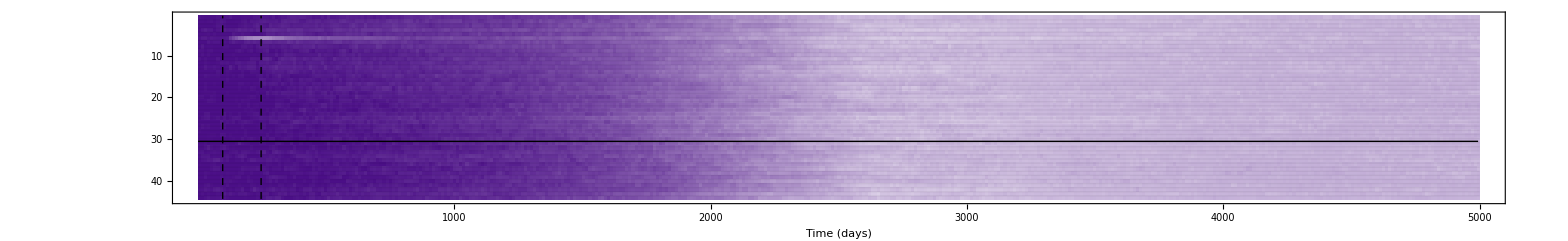
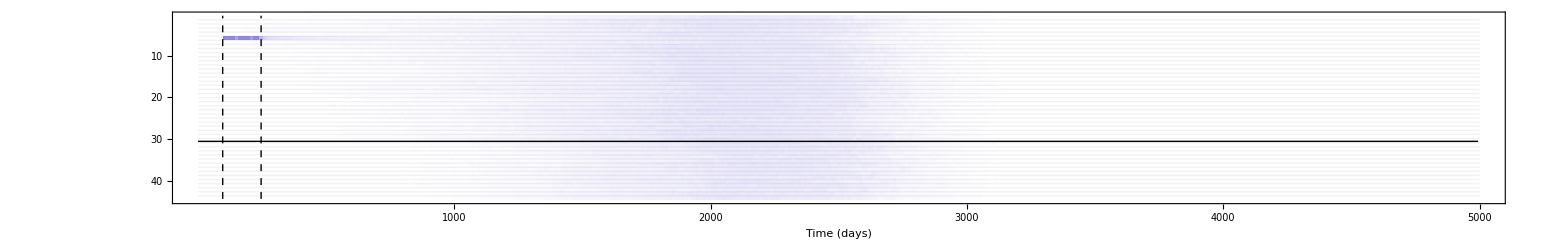
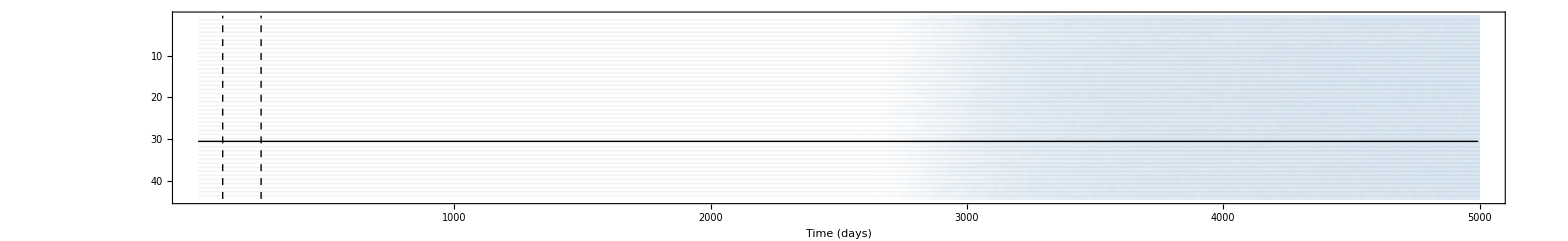
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
genotypesPlotsSuppression=Table[
frameTicks={{Automatic,None},{Automatic,Automatic}};
MatrixPlot[Transpose[aggregatedPopulations][[All,All,indicesSelection[[i]]]]//Transpose
,AspectRatio->1/6.5
,Frame->True
,FrameStyle->Directive[Black,Thick]
,ImageSize->2000
,FrameTicks->frameTicks
,FrameTicksStyle->Directive[Black,50]
,PlotRangePadding->None
,Mesh->{44,0}
,MeshStyle->Directive[Opacity[.05]]
,ColorFunction->(Blend[{White,colorPalette[[i+1]]},1.5*#1/popMax]&)(*ColorData[{"CherryTones",{1*breakdowns//Flatten//Max,0}}]*)
,ColorFunctionScaling->False
,Epilog->{Thick,Line[{{0,44-30},{416.5,44-30}}],Dashed,Line[{{8,.25},{8,44}}],Line[{{20.5,.25},{20.5,44}}]}
,FrameLabel->{{Style["Time (days)",50],Style["Time (days)",50]},{Style["\n",35],None}}
]
,{i,1,indicesSelection//Length}];
bleedSuppression=genotypesPlotsSuppression
```

## Grid

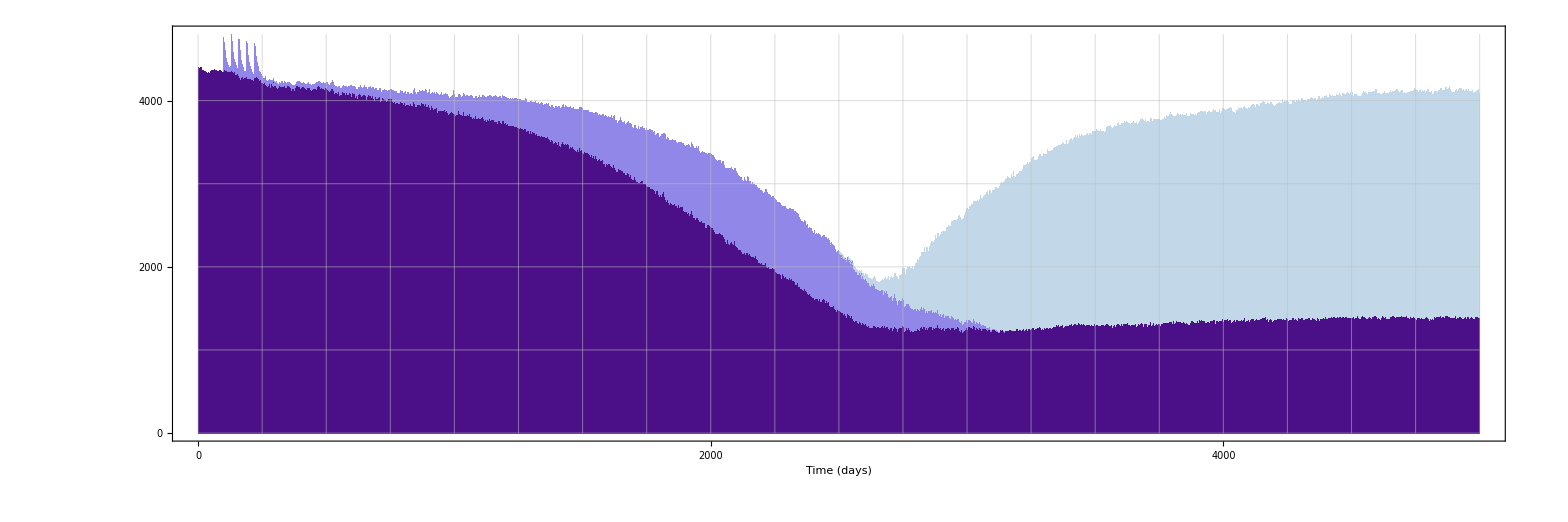
Population Size | -Graphics- | 
 |  | 
 | -Graphics- | W Allele
Metapopulation | -Graphics- | H Allele
 | -Graphics- |          R Allele

```mathematica
bleedPlots=Append[Show[#,FrameTicks->False,Frame->False,ImagePadding->{{45,19},{22.5,2.5}}]&/@bleedSuppression[[1;;3]],Show[bleedSuppression[[4]],ImagePadding->{{45,19},{22.5,2.5}}]];
gridSuppression=Grid[{
{Rotate[Style["Population Size",50,FontFamily->"Arial"],90Degree],barChartPopDynSuppression[[1]]//Show[#,ImageSize->2000,ImagePadding->{{120,60},{125,10}}]&,""},
{},
{Rotate[Style["",40,FontFamily->"Arial"],90Degree],bleedSuppression[[1]]//Show[#,ImagePadding->{{120,60},{2.5,2}}]&,Rotate[Style["W Allele",45,FontFamily->"Arial"],90Degree]},
{Rotate[Style["Metapopulation",50,FontFamily->"Arial"],90Degree],bleedSuppression[[2]]//Show[#,ImagePadding->{{120,60},{2.5,2}}]&,Rotate[Style["H Allele",45,FontFamily->"Arial"],90Degree]},
{Rotate[Style["",40,FontFamily->"Arial"],90Degree],bleedSuppression[[3]]//Show[#,ImagePadding->{{120,60},{125,2}}]&,Rotate[Style["         R Allele",45,FontFamily->"Arial"],90Degree]}
(*{Rotate[Style["2.d",60],90Degree],bleedReplacement[[4]]//Show[#,ImagePadding->{{45,19},{2.5,2.5}}]&},*)
(*{Rotate[Style["Total",40],90Degree],Show[ImageMultiply@@(Rasterize[#,RasterSize->2000,ImageResolution->10000]&/@bleedPlots),ImageSize->2000]}*)
}
,Frame->{
None,None,
{
{{1,1},{1,2}}->True,
{{2,5},{1,2}}->True
}
}
,FrameStyle->Directive[Opacity[0],LightGray,Thick]
]
```

Both

```mathematica
Grid[{Style[#,75,LineBreakWithin->False]&/@{"Population Replacement","\t","Population Suppression"},{gridReplacement,"\t",gridSuppression}}];
Export["FlowAndBleed.pdf",%,ImageSize->5000]
```

FlowAndBleed.pdf